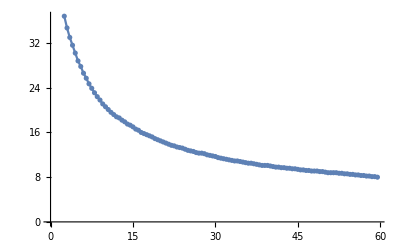

```mathematica
P={51.1,47.7,44.6,41.6,39.1,36.8,34.7,33.0,31.6,30.2,28.8,27.8,26.6,25.7,24.7,23.9,23.1,22.4,21.8,21.1,20.6,20.1,19.6,19.2,18.8,18.6,18.2,17.9,17.5,17.3,17.0,16.6,16.4,16.0,15.8,15.6,15.4,15.2,14.9,14.7,14.5,14.3,14.1,13.9,13.7,13.6,13.4,13.3,13.2,13.0,12.8,12.7,12.6,12.4,12.3,12.3,12.2,12.0,11.9,11.8,11.7,11.5,11.4,11.3,11.2,11.1,11.0,10.9,10.9,10.8,10.7,10.6,10.5,10.5,10.4,10.3,10.2,10.1,10.1,10.1,10.0,9.9,9.8,9.8,9.7,9.7,9.6,9.6,9.5,9.5,9.4,9.3,9.3,9.2,9.2,9.1,9.1,9.1,9.0,9.0,8.9,8.8,8.8,8.8,8.8,8.7,8.7,8.6,8.6,8.5,8.5,8.4,8.4,8.3,8.3,8.2,8.2,8.1,8.1,8.0};
t={0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12,12.5,13,13.5,14,14.5,15,15.5,16,16.5,17,17.5,18,18.5,19,19.5,20,20.5,21,21.5,22,22.5,23,23.5,24,24.5,25,25.5,26,26.5,27,27.5,28,28.5,29,29.5,30,30.5,31,31.5,32,32.5,33,33.5,34,34.5,35,35.5,36,36.5,37,37.5,38,38.5,39,39.5,40,40.5,41,41.5,42,42.5,43,43.5,44,44.5,45,45.5,46,46.5,47,47.5,48,48.5,49,49.5,50,50.5,51,51.5,52,52.5,53,53.5,54,54.5,55,55.5,56,56.5,57,57.5,58,58.5,59,59.5};
data1=Table[{t[[i]],P[[i]]},{i,1,120}];
pd=ListPlot[data1];
pdl=ListLinePlot[data1];
Show[pd,pdl]
```

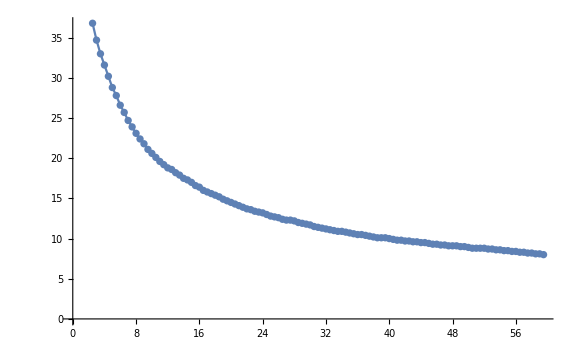

```mathematica
Show[%40,ImageSize->Large]
```

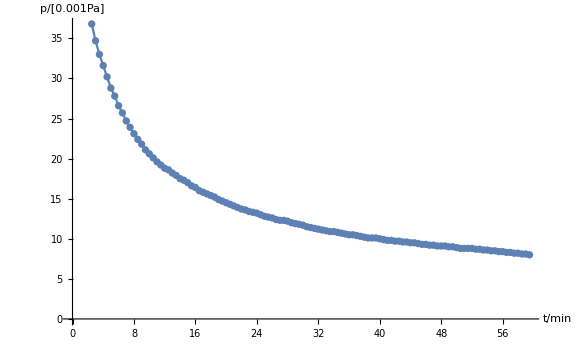

```mathematica
Show[%41,AxesLabel->{HoldForm[t/min],RawBoxes[FractionBox["p",RowBox[{"[",RowBox[{"0.001`","Pa"}],"]"}]]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

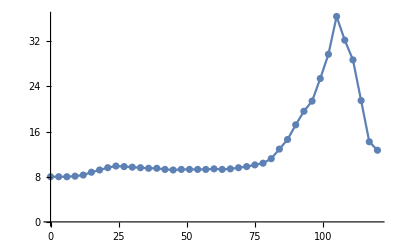

```mathematica
p2={8.0,8.0,8.0,8.1,8.3,8.8,9.2,9.6,9.9,9.8,9.7,9.6,9.5,9.5,9.3,9.2,9.3,9.3,9.3,9.3,9.4,9.3,9.4,9.6,9.8,10.1,10.4,11.2,12.9,14.6,17.2,19.6,21.4,25.4,29.7,36.4,32.2,28.7,21.5,14.2,12.7};
data2=Table[{3*(i-1),p2[[i]]},{i,1,41}];
pd2=ListPlot[data2];
pdl2=ListLinePlot[data2];
Show[pd2,pdl2]
```

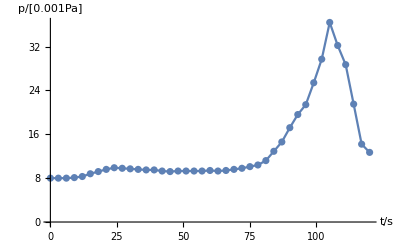

```mathematica
Show[%61,AxesLabel->{HoldForm[t/s],RawBoxes[RowBox[{"p","/",RowBox[{"[",RowBox[{"0.001","Pa"}],"]"}]}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

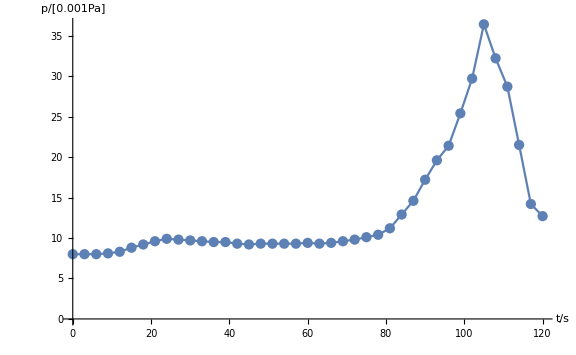

```mathematica
Show[%62,ImageSize->Large]
```

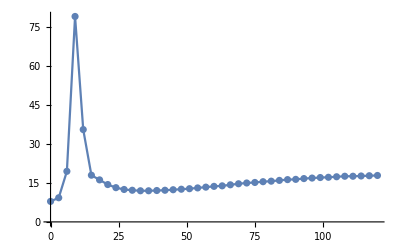

```mathematica
p3={7.9,9.3,19.5,79.2,35.6,18.0,16.2,14.4,13.2,12.5,12.2,12.0,12.0,12.1,12.2,12.4,12.6,12.8,13.1,13.4,13.7,13.9,14.3,14.7,15.0,15.2,15.5,15.7,16.0,16.3,16.4,16.7,16.9,17.1,17.2,17.4,17.6,17.6,17.7,17.8,17.9};
data3=Table[{3*(i-1),p3[[i]]},{i,1,41}];
pd3=ListPlot[data3,PlotRange->All];
pdl3=ListLinePlot[data3,PlotRange->All];
Show[pd3,pdl3]
```

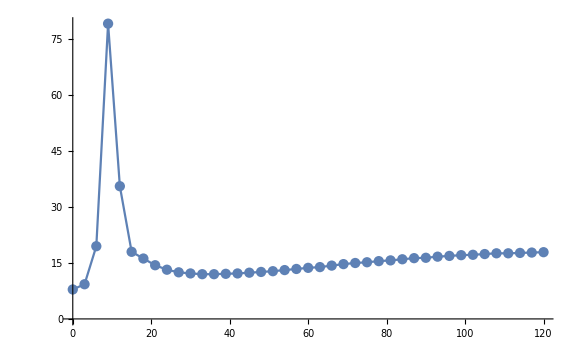

```mathematica
Show[%132,ImageSize->Large]
```

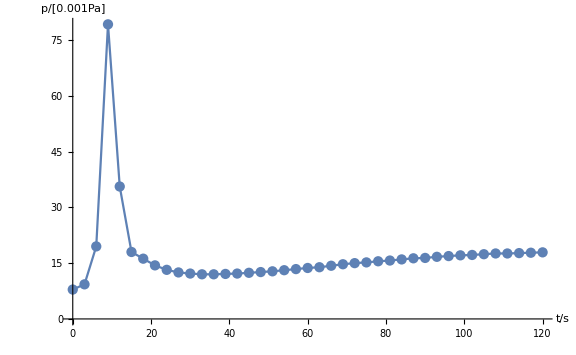

```mathematica
Show[%133,AxesLabel->{HoldForm[t/s],RawBoxes[RowBox[{"p","/",RowBox[{"[",RowBox[{"0.001","Pa"}],"]"}]}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```